## The Basics

Please click on the » to open collapsed sections.

## Learning Objectives

This section will familiarize users with the different features of Wolfram Notebooks and help them become comfortable with working in notebooks.

### Work with Wolfram Notebooks

Open a notebook in the Wolfram Cloud

Add content to a notebook

Text

Code

Image

Interactivity

Cells

Write and evaluate code

Shift+Enter to evaluate

Suggestions Bar

Save and share notebooks

Download a notebook to the desktop and continue to work on it offline

### Know the User-Friendly Features of Notebooks

The notebook toolbar

Syntax coloring

Autocompletion

Getting help

Computation using natural language

### Edit a Simple Notebook

Evaluate existing code

Modify and reevaluate changes

### Browse Examples of Published Wolfram Notebooks

## A Notebook in the Cloud

-Graphics-

## What Can a Notebook Contain?

Open a new notebook and try adding content to it.

### Wolfram Language Code

```mathematica
2+2
```

4

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

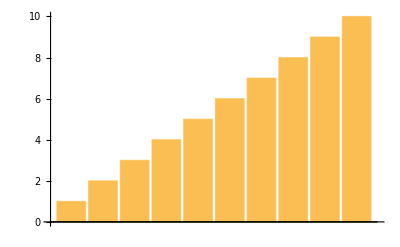

```mathematica
BarChart[Range[10]]
```

### Text

Calculate the result of adding 2 and 2:

```mathematica
2+2
```

4

Create a list of numbers from 1 to 10:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Create a bar chart for the numbers in the preceding list:

```mathematica
BarChart[Range[10]]
```

-Graphics-

### Images and Graphics

Get the image of a gray wolf (press = and type in “image of a gray wolf”):

WolframAlphaQueryParseResults

-Graphics-

Copy and paste an image from a website:

```mathematica
SystemOpen["https://www.wolfram.com/featureset/machine-learning/"]
```

Import an image from the Wolfram website:

```mathematica
Import["https://www.wolfram.com/featureset/notebooks/img/wolfie.png"]
```

-Graphics-

Import an image from your computer:

```mathematica
Import[FileNameJoin[{NotebookDirectory[],"data","Rosa_Precious_platinum.jpg"}]]
```

-Graphics-

Visualize a function:

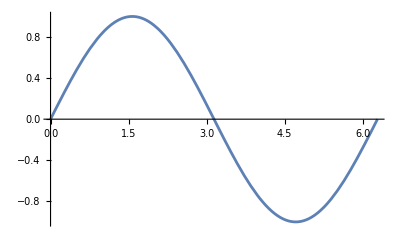

```mathematica
Plot[Sin[x],{x,0,2 π}]
```

Create a very simple graphic:

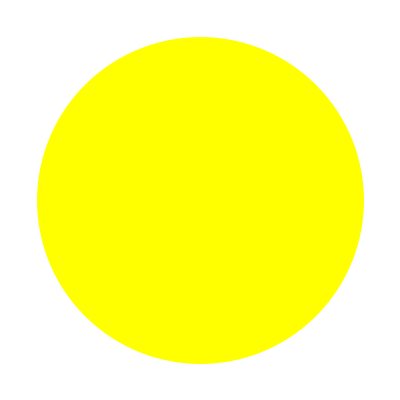

```mathematica
Graphics[{Yellow,Disk[]}]
```

### Interactivity

Create concentric yellow and black disks such that the diameter of the black inner disk can be controlled interactively with a slider:

```mathematica
Manipulate[Graphics[{Yellow,Disk[],Black,Disk[{0,0},r]}],{r,0,1}]
```

So a notebook can contain code (input and output), text explanations, images, graphics and a host of other things.

## Cells in a Notebook

A notebook is a structured document.

The structure is delineated by the “cell.”

Cells typically have distinct brackets on the right.

A cell may contain narrative text, code, math, images or some combination.

-Graphics-

You can cut, copy and paste cells with standard keyboard shortcuts. To delete a cell, select the cell bracket and press the Delete button.

## Different Styles of Cells

### Creating a New Cell

Everything you type into the notebook is entered into a cell. To create a new cell, click anywhere in the notebook and start typing. By default, a new cell will have the “Input” style—meant for Wolfram Language input.

-Graphics-

### Text and Other Styles

But you can enter other styles of input. Click the little plus sign that shows up at the head of the horizontal line across the notebook, when you click anywhere in the notebook. From the style menu that appears, select Plain Text to add text notes to your notebook:

-Graphics-

-Graphics-

You can also have other styles of text, like Title, Section and so on.

It is possible to change the style of existing text from the Format menu. Just select the cell and update the style: Format ▶ Style.

Most of the common styles have keyboard shortcuts for ease of use: Cmd+9 (or Alt+9) for input, Cmd+7 (or Alt+7) for text, Cmd+4 (or Alt+4) for Section, etc.:

-Graphics-

## Cell Groups

### Opening and Closing Cell Groups

Cell brackets show the hierarchical grouping of cells. By default, some cell styles automatically group other styles. You can double-click the outermost bracket that spans a cell group to close the group.

To expand a closed cell group, you can click the cell opener » or double-click the outermost cell bracket again.

### Reverse-Closing a Cell

By the way, if you only want to show the output of a computation while hiding the input, you can reverse-close a cell by double-clicking the cell bracket of the output cell:

```mathematica
Import["https://www.wolfram.com/featureset/notebooks/img/wolfie.png"]
```

-Graphics-

## Writing and Evaluating Code

Here are a few things you will find useful to know while writing code in Wolfram notebooks.

### Shift+Enter to Evaluate

To evaluate Wolfram Language code in a notebook, click inside the notebook, type in the code and then press the Shift+Enter keys on the keyboard:

```mathematica
2+2
```

4

### Suggestions Bar

Along with the output of your computation, you will see the Suggestions Bar appear. It provides immediate access to possible next steps, optimized for your results:

-Graphics-

You can select a function from among these suggestions. Or, if you know exactly what you want to do next, you can turn off the Suggestions Bar.

## Saving and Sharing Notebooks

### Save in the Cloud

Notebooks are automatically saved in the cloud. You can also specify the name you want.

Notice the file extension is .nb:

-Graphics-

### Click to Publish or Share

Click Publish to publish your notebook to the web so everyone can read it:

-Graphics-

To share the notebook with a specific set of people, click Share:

-Graphics-

With Wolfram Notebooks, you have a really easy way to get rich, interactive, computational content onto the web.

## From the Cloud to the Wolfram Desktop

Download the cloud notebook to Wolfram Desktop or Mathematica and continue working on it.

(Here are the instructions to download and install Wolfram Desktop.)

-Graphics-

-Graphics-

## User-Friendly Features of the Notebook Interface

As you continue to work in the notebook, here are a few more tips to make it easier to use the notebook for programming in Wolfram Language.

### A Toolbar for Every Notebook

-Graphics-

Starting with Version 13.1 of Wolfram Language, a toolbar is displayed by default in every standard notebook. The toolbar has buttons like  for “Evaluate” (equivalent to pressing Shift+Enter),  to “Abort or stop a computation, -Graphics- to select what type of cell you want to insert, for a panel to control the appearance of cells and so on for users to conveniently execute often-used operations by “pressing a button.” The tooltip for each button explains its use.

### Syntax Coloring: Blue versus Black

When you start typing something in an input cell, the text appears in blue until the Wolfram Language kernel is able to recognize the term. Once recognized, it turns black:

```mathematica
Ran
```

```mathematica
RandomInteger
```

### Autocomplete

What if you do not know the name of the Wolfram Language function already? As you start typing the first few letters, you will see a context-sensitive autocompletion menu pop up with names of functions beginning with the letters you have typed in. Simply select the function you need from this list:

-Graphics-

If you hover over the name of a function, a little popup appears:

-Graphics-

Clicking the down arrow brings up a list of templates showing the syntax for using this function. (You can use the shortcut keys Cmd+Shift+K after typing in a function name to get to this list.):

-Graphics-

Select the template you need, and it will appear in the notebook with yellow placeholders that can be filled in:

```mathematica
RandomInteger[{Subscript[i, min],Subscript[i, max]}]
```

### Getting Help

For more information on a function, hover over the function name and click the “i”:

-Graphics-

This opens the documentation page for the function:

-Graphics-

You can highlight a word and press the F1 key (on Windows) or CmdShiftF (on macOS) to go directly to the documentation page on that symbol.

You can also access the documentation at any time from Help ▶ Wolfram Documentation and browse the topics and examples there:

-Graphics-

## Using Natural Language for Computations

Notebooks also act as an interface for you to perform computations using natural language.

To enter a natural language input for computation, start by typing the equal sign:

WolframAlphaQueryParseResults

5840504 people

You can also query the Wolfram|Alpha knowledgebase from the notebook. For this, start with ==:

denmark

The notebook can also convert natural language input into Wolfram Language entities.

Type Ctrl=, then type your natural language input inside the little gray box and press Enter. Your input will be interpreted as a Wolfram Language entity:

-Graphics-→   → -Graphics-

You can now ask for the properties of this entity and use them for computation.

As you start typing in the name of the property, a list will appear in the autocomplete menu. Autocompletion has been built into the interface to help the user whenever possible:

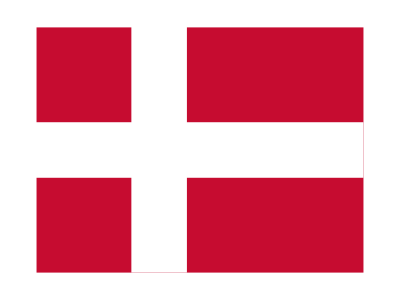

```mathematica
Entity["Country","Denmark"]["Flag"]
```

```mathematica
Entity["Country","Denmark"]["AdministrativeDivisions"]
```

{Hovedstaden, Denmark,Midtjylland, Denmark,Nordjylland, Denmark,Sjaælland, Denmark,Syddanmark, Denmark}

Type in = and then type in “population of Denmark’s administrative regions”:

WolframAlphaQueryParseResults

{1822659 people,1304253 people,589148 people,820480. people,1205728 people}

```mathematica
EntityValue[Entity["Country","Denmark"][EntityProperty["Country","AdministrativeDivisions"]],EntityProperty["AdministrativeDivision","Population"]]
```

{1822659 people,1304253 people,589148 people,820480. people,1205728 people}

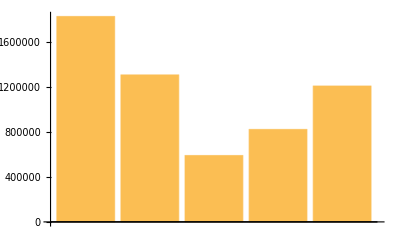

```mathematica
BarChart[EntityValue[Entity["Country","Denmark"][EntityProperty["Country","AdministrativeDivisions"]],EntityProperty["AdministrativeDivision","Population"]]]
```

Note: If you have a keyboard layout that makes it difficult to enter Ctrl=, this post may be helpful.

## Working in a Wolfram Notebook

Now it is time to have some fun experimenting with Wolfram Language in a notebook. Try editing this colorful notebook yourself.

Click Make Your Own Copy on the top-right corner to create your own copy of the notebook to edit.
-Graphics-

Edit the heading "Something Colorful" to say something more meaningful to you.

Replace the image of the frog with a different image.

Evaluate the line of code with ImageIdentify[...] by placing your cursor anywhere in the cell and pressing Shift+Enter.

Evaluate the line of code that says WordDefinition[%].

Place your cursor in the empty space in the notebook after the output from the preceding line of code and type in Length[TextWords[%]].

Evaluate the code you just typed in—it should give you the number of the words in the line of text from the previous output.

## Neat Examples of Notebooks

Here are a few “finished” notebooks:

Computational essay on the Central Limit Theorem by Stephen Wolfram

Blog post on Analyzing Social Networks of Colonial Boston Revolutionaries with the Wolfram Language by Swede White

A quick exploration of some social media analytics, with examples using a personal Twitter account

A Wolfram U webinar announcement, published online

More examples of notebooks available at:

https://www.notebookarchive.org

https://demonstrations.wolfram.com

https://www.wolfram.com/wolfram-u

## References

Wolfram Computational Notebooks

The New World of Notebook Publishing by Stephen Wolfram

Introduction to Wolfram Notebooks—a full interactive course on Wolfram U

Tutorial on Using a Notebook Interface

How to | Select and Type in Notebooks

Tutorial on Doing Computations in Notebooks

How to | Manage Computations in Notebooks

Notebook Documents—from A Fast Introduction for Programmers